```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Verdana",FontSize->12}];
```

```mathematica
foil={{0,-5},{18,8},{39.5,20},{60,29},{79,33},{90,31},{100,25},{102,16},{100,10},{91,4},{85,3},{67.5,3},{42.5,2},{19.5,-1},{0,-5}};
val={{0,0},{18,-0.1},{39.5,-1.0},{60,-5.6},{79,-14.6},{90,-13},{100,0.5},{102,15.5},{100,5.4},{91,-8.8},{85,-7.5},{67.5,-0.8},{42.5,2.3},{19.5,1.5},{0,0}};
```

```mathematica
up={{0,-0.1},{18,-0.1},{39.5,-1.0},{60,-5.6},{79,-14.6},{90,-13},{100,0.5},{102,15.5}};
low ={{102,15.5},{100,5.4},{91,-8.8},{85,-7.5},{67.5,-0.8},{42.5,2.3},{19.5,1.5},{0,1.5}}//Reverse;
```

```mathematica
pup=ListPlot[up,PlotStyle->{Thick,Darker[Green]},PlotMarkers->Automatic];
plow=ListPlot[low,PlotStyle->{Thick,Red},PlotMarkers->Automatic];
Show[pup,plow,AxesLabel->{"x [mm]","Pressure [mmWs]"}];
```

```mathematica
order:=1;
uint=Interpolation[up,InterpolationOrder->order];
lint=Interpolation[low,InterpolationOrder->order];
ip=Plot[{uint[x],lint[x]},{x,0,102},PlotStyle->{{Thick,Darker[Green]},{Thick,Red}},Filling->{1->{2}},FillingStyle->{Lighter[Gray,0.8]}];
intdiff=0.01*9.81*0.001*NIntegrate[lint[x]-uint[x],{x,0,102}]
```

0.0438752

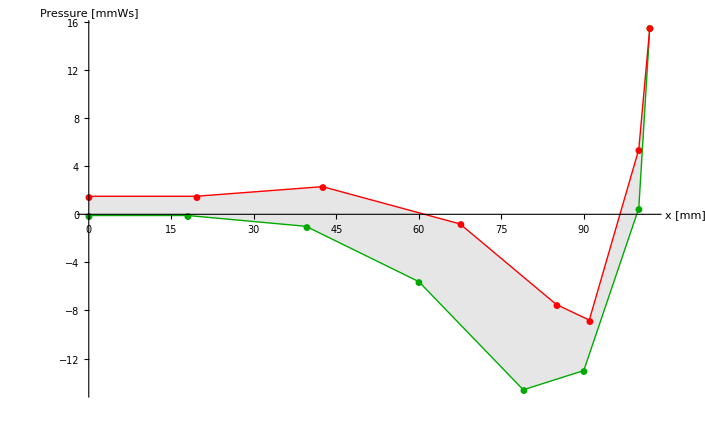

```mathematica
Show[ip,pup,plow,AxesLabel->{"x [mm]","Pressure [mmWs]"}]
```